Biological Modelling and Model Analysis - day II

Exploring Different Modelling Formalisms (1)

Sander van Doorn

Groningen Institute for Evolutionary Life Sciences

g.s.van.doorn@rug.nl

## Stochastic simulation of a metapopulation

Metapopulation models were developed to study the dynamics of populations in fragmented habitats. In their simplest version, the population is distributed over many small habitat patches; each patch is considered to be either empty or occupied (the model does not keep track of the number of individuals within each patch), and patches are colonised from a global migrant pool (i.e., spatial relationships between patches are not taken into consideration).

The code below implements a metapopulation model for two interacting species that compete for space. Species 1 is a superior competitor: when it arrives at a patch that is already occupied, it displaces the other species. Species 2 is a superior coloniser: its has a higher rate of dispersal, allowing it to colonise empty patches faster. For simplicity, both species are assumed to have the same rate of local extinction.

```mathematica
simulateMetaPop[e_,c1_, c2_,T_:100,n_:100]:=Module[{S,x0,f,i,state,freq,data,pl1,pl2},
(* initialise metapopulation *)
x0=Quotient[n,10];
S=Join[Table[1,x0],Table[2,x0]];
S=Join[Table[0,n-Length[S]],S];
f={x0/n,x0/n};
data=Reap[Sow[S,state];
Sow[f,freq];
Do[
(* step 1 : extinction of patches *)
S=(If[RandomReal[]<e,0,#])&/@S;
(* step 2 : colonisation of patches by species 2 *)
If[f[[2]]>0,S=(If[#==0 &&RandomVariate[PoissonDistribution[c2 f[[2]]]]>0,2,#])&/@S];
(* step 3 : colonisation of patches by species 1 *)
If[f[[1]]>0,S=(If[(#==0 || #==2)  &&RandomVariate[PoissonDistribution[c1 f[[1]]]]>0,1,#])&/@S];
(* determine new frequencies *)
f={Count[S,1]/n,Count[S,2]/n};
(* store data *)
Sow[S,state];
Sow[N[f],freq],{i,1,T}]][[2]];
(* create plots *)
pl1=MatrixPlot[Transpose[data[[1]]],ColorRules->{0->Yellow,1->Darker[Red],2->Darker[Blue]}];
pl2=ListPlot[Transpose[data[[2]]],Joined->True,PlotStyle->{Darker[Red],Darker[Blue]},Frame->True,PlotRange->All];
GraphicsRow[{pl1,pl2},ImageSize->Large]
]
```

Here are a few hints to help you understand the code:

Hint (1) the update of the state of the metapopulation is implemented by a Do[] statement, one of Mathematica's statements for building iterative procedures. Its syntax is illustrated below:

```mathematica
Do[Print["t = ",t],{t,0,5}]
```

t = 0

t = 1

t = 2

t = 3

t = 4

t = 5

Hint (2) the update rules for the individual patches are stochastic and are implemented by calling functions that generate (pseudo-)random numbers. You can verify that these funcions produce different results (numbers drawn from a particular probability distribution)  when they are called repeatedly:

```mathematica
Table[RandomReal[],10]
Table[RandomVariate[PoissonDistribution[5.0]],10]
```

{0.724315,0.323661,0.912487,0.563192,0.952266,0.661156,0.366016,0.668904,0.410564,0.524116}

{5,4,2,2,2,6,5,3,6,2}

Hint (3) cells are updated by applying a series of three update steps to the list S, which contains the states of individual patches. To apply a function to each element in a list, you can call the Mathematica function Map[], or apply its shorthand form /@.

```mathematica
xValues=Table[i,{i,1,5}];
f[x_]:=x^2
Map[f,xValues]
f/@xValues
```

{1,4,9,16,25}

{1,4,9,16,25}

Instead of defining the function f[] first, you can also write it in “pure function form”. To do this, take the right-hand side of the function, replace all x’s by the argument placeholder #, enclose everything in braces, and write & at the end. In other words, the “pure function form” of f[x_]:=x^2 is  (#^2)&, so that we can square all elements in a list by writing:

```mathematica
(#^2)& /@xValues
```

{1,4,9,16,25}

Hint (4) data are collected during the simulation using the Reap[Sow[]] construction. Here, we are collecting two kinds of information, the cell states and the frequencies of patches occupied by species 1 and 2, which are stored in separate lists using distinct labels state and freq.

```mathematica
Reap[
Sow["R",list1];
Sow["S",list2];
Sow["e",list1];
Sow["a",list1];
Sow["o",list2];
Sow["w",list2];
Sow["p",list1];
][[2]]
```

{{R,e,a,p},{S,o,w}}

The procedure simulateMetaPop[] generates two plots. On the left is a MatrixPlot[] that shows the state of individual patches of the metapopulation over time; on the right are the frequencies of the patches occupied by species 1 and 2 (red and blue, respectively). The simulation below shows that the two species can coexist in the metapopulation, even though the red species is a superior competitor.

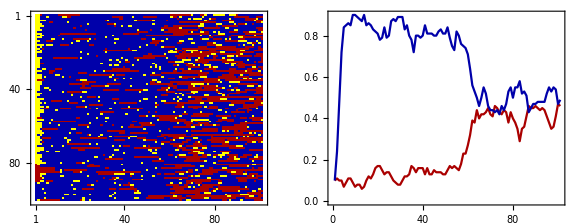

```mathematica
simulateMetaPop[0.2, 0.3, 2.0,100,100]
```

Q1: Why is it that the inferior competitor can maintain such high frequency? Predict what will happen if you change the extinction rate or the dispersal advantage of species 2.

Q2: Test your hypotheses by running additional simulations

## ODE version of the metapopulation model

An alternative approach to modelling a metapopulation is to write ODEs that capture the change of the frequencies of patches occupied by species 1 (p[t]) and species 2 (q[t]).

Q3: Derive such equations, under the assumption that the number of metapopulation patches is very large and that extinction and colonisation occur continuously in time. Explain why these assumptions are necessary.

```mathematica
eqp:=D[p[t],t]==Subscript[c, 1] p[t](1-p[t])-e p[t]
eqq:=D[q[t],t]==Subscript[c, 2] q[t](1-p[t]-q[t])-e q[t]-Subscript[c, 1] q[t]p[t]
```

Next, determine the equilibria of your model:

```mathematica
rhsp=eqp[[2]]/.{p[t]-> P,q[t]->Q};
rhsq=eqq[[2]]/.{p[t]-> P,q[t]->Q};
equilibria=Solve[{rhsp==0,rhsq==0},{P,Q}]//Simplify
```

{{P→0,Q→1-e/c_2},{P→1-e/c_1,Q→e/c_1-c_1/c_2},{P→1-e/c_1,Q→0},{P→0,Q→0}}

and assess their stability

```mathematica
(J=D[{rhsp,rhsq},{{P,Q}}]/.equilibria[[1]])//MatrixForm
Eigenvalues[J]
```

(-e+c_1 | 0
-c_1 (1-e/c_2)-(1-e/c_2) c_2 | -(1-e/c_2) c_2)

{-e+c_1,e-c_2}

Q4: Under what conditions can both species coexist in the metapopulation?

One way to answer this question is to check for what range of extinction rates both species can coexist at positive frequencies:

```mathematica
Reduce[0<P<1&&0<Q<1/.equilibria[[2]]/.{Subscript[c, 1]->0.3,Subscript[c, 2]->2.0},e]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.045<e<0.3

Q5: How do these conditions compare to the results of the stochastic metapopulation model? Explain potential discrepancies.

The two versions of the model give very comparable outcomes if the number of patches is sufficiently large and the rates of colonisation and extinction are low (so it is unlikely that more than a single event occur per timestep).